# Comparing SSA model to experimental results

Code for forecasting extinction risk under different levels of temporal autocorrelation for a specific time series and time scale. This notebook contains all the code used to generate the simulations and create Fig. 5; for easy replication of that figure, download the required MX files from the repository beforehand (files). Subfigures from this notebook were compiled using Adobe Illustrator 2024.

## Background Functions

Run this section once to define the TPC and the necessary functions for the SSA model. Before running, define the directory you want to import to or export from.

```mathematica
directory="/directory/";

(*parameters for K and lactin2 model fit*)
K=5000;
a=0.044;
b=-1.774;
tmax=35.254;
deltat=5.435;

(*lactin2 equation*)
netgrowth[temp_]:=Module[
{a=0.044,
b=-1.774,
tmax=35.254,
deltat=5.435,
est},
est=Exp[a*temp]-Exp[a*tmax-((tmax-temp)/deltat)]+b;
est
];

(*define birth function*)
bTemp[temp_]:=Module[
{a=0.044,
birth},
birth=Exp[a*temp];
birth
];
rmax=FindMaximum[netgrowth[x],x];
topt=x/.rmax[[2]];
rmax=rmax[[1]];
d1=netgrowth[topt]/K;

(*define death function, adjusted so that K declines over time*)
dTemp[temp_,n_,t_]:=Module[
{a=0.044,
b=-1.774,
tmax=35.254,
deltat=5.435,
topt=25.0341,
d1=0.000103037},
Exp[a*tmax-((tmax-temp)/deltat)]-b+(d1+d1*t/56)*n
];

(*calculate persistence boundaries*)
lactin2[T_,{a_,b_,tmax_,δT_}]:=Exp[a T]-Exp[a tmax-((tmax-T)/δT)]+b;
paramsfit={0.044,-1.774,35.254,5.435};
w[T_]:=lactin2[T,paramsfit];
divisions=40;
σTrange=Range[0.01,8.01,8/divisions];
μTrange=Range[10,35,25/divisions];

Clear[T];
moments=Flatten[ParallelTable[Module[{mean,var,skew,kurt},
mean=NExpectation[w[T],T\[Distributed]NormalDistribution[μT,σT]];
var=NExpectation[(w[T]-mean)^2,T\[Distributed]NormalDistribution[μT,σT]];
skew=NExpectation[((w[T]-mean))^3,T\[Distributed]NormalDistribution[μT,σT]]/var^(3/2);
kurt=NExpectation[(w[T]-mean)^4,T\[Distributed]NormalDistribution[μT,σT]]/(var^2)-3;
{μT,σT,mean,var,skew,kurt,If[mean>0,Log10[var/mean],10]}],{σT,σTrange},{μT,μTrange}],1];
```

## SSA Model

Run simulations and store extinction outcomes. Choose which temperature time series to use by changing the value of ‘series’ (temps = white noise, temps2 = pink noise, temps3 = brown noise). The SSA occurs in the ParallelDo loop over the parameters specified in ‘μTrange’ and ‘σTrange.’ This code is quite slow; if you have already downloaded the MX files, skip to the next block of code.

```mathematica
(*experimental temperature time series*)
tempsequence={28.105,20.9738,21.7771,31.756,28.6008,28.3445,28.4703,23.9669,30.6391,24.6075,27.7707,30.1283,24.8433,24.1295,23.2893,27.3607,32.3506,20.818,25.63,25.3925,29.9094,23.1105,25.0783,26.2814,25.2352,24.9217,25.5506,26.0331,26.4504,16.71,23.5496,22.7367,21.6555,24.0484,26.198,29.3465,33.29,30.9471,25.,24.21,24.5286,26.7995,23.6345,20.6535,28.2229,28.878,18.6904,19.6306,25.1567,27.46,21.2635,25.3137,22.8324,25.9516,26.623,19.0529,22.3352,26.3655,25.4714,26.1152,23.802,27.2633,23.2005,27.5613,25.7098,34.1517,17.6494,22.0094,20.2919,22.4387,26.7107,31.3096,21.3992,23.4638,22.2293,21.5297,24.7648,26.5362,24.2902,29.5213,28.7365,18.244,24.6863,19.3609,29.0262,23.0192,21.895,27.6648,25.79,30.3694,21.122,27.1676,22.9265,24.4494,20.4787,26.8895,22.1208,25.8705,26.9808,27.8792,27.0735,23.7186,27.9906,29.182,22.6393,23.377,24.37,23.8848,19.8717,29.7081,20.0906,22.54};
tempsequence2={19.6306,20.818,21.122,23.7186,28.3445,29.3465,27.6648,27.0735,24.7648,30.3694,27.5613,27.46,26.1152,27.1676,24.0484,25.4714,25.8705,23.0192,26.4504,29.7081,25.63,32.3506,26.9808,25.3137,28.878,22.7367,29.182,29.9094,26.7995,25.3925,22.4387,23.4638,24.2902,25.1567,24.9217,22.9265,26.623,27.8792,23.2893,22.6393,20.4787,23.9669,25.5506,24.5286,19.8717,26.8895,26.2814,29.5213,31.756,31.3096,26.5362,34.1517,30.1283,28.6008,33.29,29.0262,28.7365,28.2229,28.4703,24.21,24.4494,30.9471,25.,27.2633,25.9516,23.377,21.895,24.6863,24.8433,24.6075,20.0906,21.5297,25.79,23.1105,21.3992,17.6494,22.54,22.3352,25.2352,21.2635,26.3655,18.6904,20.2919,24.37,23.6345,25.0783,23.5496,22.2293,21.7771,22.0094,22.1208,19.0529,16.71,18.244,21.6555,23.2005,24.1295,27.3607,23.802,19.3609,20.6535,25.7098,26.7107,26.198,28.105,30.6391,23.8848,26.0331,27.9906,27.7707,20.9738,22.8324};
tempsequence3={22.9265,22.8324,23.377,23.6345,23.802,23.8848,25.1567,24.6863,23.2893,22.4387,21.895,20.4787,20.9738,21.6555,20.0906,21.3992,20.6535,22.2293,23.2005,23.5496,25.2352,26.3655,25.63,25.7098,24.6075,24.2902,22.54,24.0484,24.4494,23.4638,24.9217,25.,23.7186,23.1105,22.7367,22.1208,22.3352,21.5297,21.2635,19.3609,19.6306,18.6904,18.244,16.71,17.6494,19.0529,20.2919,20.818,21.7771,21.122,19.8717,22.0094,23.0192,24.1295,25.3137,26.2814,25.9516,26.0331,27.5613,26.8895,26.4504,25.79,26.198,25.3925,26.7107,30.1283,29.9094,28.878,27.7707,28.3445,28.105,27.9906,26.5362,29.0262,29.182,30.6391,30.9471,31.3096,30.3694,32.3506,33.29,34.1517,31.756,29.7081,27.6648,28.7365,27.1676,28.2229,29.5213,26.9808,26.1152,27.2633,26.623,27.46,27.3607,27.8792,28.4703,29.3465,27.0735,25.8705,25.5506,28.6008,26.7995,25.4714,24.8433,24.7648,25.0783,23.9669,24.37,24.21,24.5286,22.6393};

(*add zero to end of each series to keep algorithm from crashing at final step*)
temps=Join[(tempsequence-25)/3.5,{0}]; (*white*)
temps2=Join[(tempsequence2-25)/3.5,{0}]; (*pink*)
temps3=Join[(tempsequence3-25)/3.5,{0}]; (*brown*)

series=temps; (*pick series here*)

(*delineate parameter range*)
divisions=40;
σTrange=Range[0.01,8.01,8/divisions]; 
μTrange=Range[10,35,25/divisions];
output={};
reps=40;(*40*)

SetSharedVariable[output];
ParallelDo[
extinct=0;
Do[
n=500;
t=0;
tcount=1;
T=series[[tcount]]*σ+μ;
Tinterval=tnext=0.5;

While[t<56,
evector={bTemp[T]*n,dTemp[T,n,t]*n};
t+=RandomReal[ExponentialDistribution[Total[evector]]];
event=RandomChoice[evector->{1,2}];
If[event==1,n++,n--];
If[n==0,extinct++;Break[]];
If[t>=tnext,tcount++;T=series[[tcount]]*σ+μ;tnext+=Tinterval]],{reps}];
If[n<10&&n!=0,extinct++];
AppendTo[output,{μ,σ,N[1-extinct/reps]}],{μ,μTrange},{σ,σTrange}];

Which[series==temps,color="white",series==temps2,color="pink",series==temps3,color="brown"];
Export[directory<>"SSA2_"<>color<>".m",output,"MX"]
```

Download the needed MX files and generate plots shown in Fig. 5a-c.

```mathematica
SSAwhite=Import[directory<>"SSA2_white.m","MX"];
SSApink=Import[directory<>"SSA2_pink.m","MX"];
SSAbrown=Import[directory<>"SSA2_brown.m","MX"];

wresults={{25.0284,3.29531,0.83333},{27.0072,3.3534,0.5},{28.0454,3.31001,0.41667},{29.0142,3.33436,0.16667},{30.0345,3.25052,0}};
presults={{24.9767,3.30643,0.91667},{26.9774,3.37776,0.75},{28.0292,3.37251,0.41667},{28.9799,3.43065,0.08333},{30.0191,3.39953,0}};
bresults={{25.0567,3.4065,1},{27.0608,3.3472,0.16667},{28.0491,3.39566,0},{29.0499,3.39271,0},{29.9115,3.44396,0}};

newmap[x_]:=Blend[{RGBColor["#ffffd9"],RGBColor["#edf8b1"],RGBColor["#c7e9b4"],RGBColor["#7fcdbb"],RGBColor["#41b6c4"],RGBColor["#4eb3d3"],RGBColor["#2b8cbe"],RGBColor["#0868ac"],RGBColor["#084081"]},1-x];

SSAwhiteplot=Show[ListContourPlot[SSAwhite,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["a)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,wresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,wresults}]}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot=Show[ListContourPlot[SSApink,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["b)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,presults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,presults}]}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot=Show[ListContourPlot[SSAbrown,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["c)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,bresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,bresults}]}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAs=GraphicsRow[{SSAwhiteplot,SSApinkplot,SSAbrownplot},Spacings->0,ImageSize->1000]
(*Export[directory<>"SSAs.pdf",SSAs,ImageResolution->1000]*)
```

-Graphics-

Generate additional plots over a longer timescale to see how the envelope of persistence contracts when tmax is greater; use to generate Fig S5.

```mathematica
SSAwhite2=Import[directory<>"SSA2_t1009_20reps_white.m","MX"];
SSApink2=Import[directory<>"SSA2_t1009_20reps_pink.m","MX"];
SSAbrown2=Import[directory<>"SSA2_t1009_20reps_brown.m","MX"];

SSAwhiteplot2=Show[ListContourPlot[SSAwhite2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0), t_max = 1009",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]](*,
Epilog->
{{Text[Style["a)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,wresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,wresults}]}*)],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot2=Show[ListContourPlot[SSApink2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1), t_max = 1009",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]](*,
Epilog->
{{Text[Style["b)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,presults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,presults}]}*)],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot2=Show[ListContourPlot[SSAbrown2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2), t_max = 1009",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]](*,
Epilog->
{{Text[Style["c)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,bresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,bresults}]}*)],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAs=GraphicsRow[{SSAwhiteplot2,SSApinkplot2,SSAbrownplot2},Spacings->0,ImageSize->1000]
(*SSAs=GraphicsGrid[{{SSAwhiteplot,SSApinkplot,SSAbrownplot},{SSAwhiteplot2,SSApinkplot2,SSAbrownplot2}},Spacings->0,ImageSize->1000]*)
Export[directory<>"SSAs_t1009.pdf",SSAs,ImageResolution->1000];
```

-Graphics-

## Compare results to the running mean

Use this code to calculate the running mean and generate Fig. 5d-f.

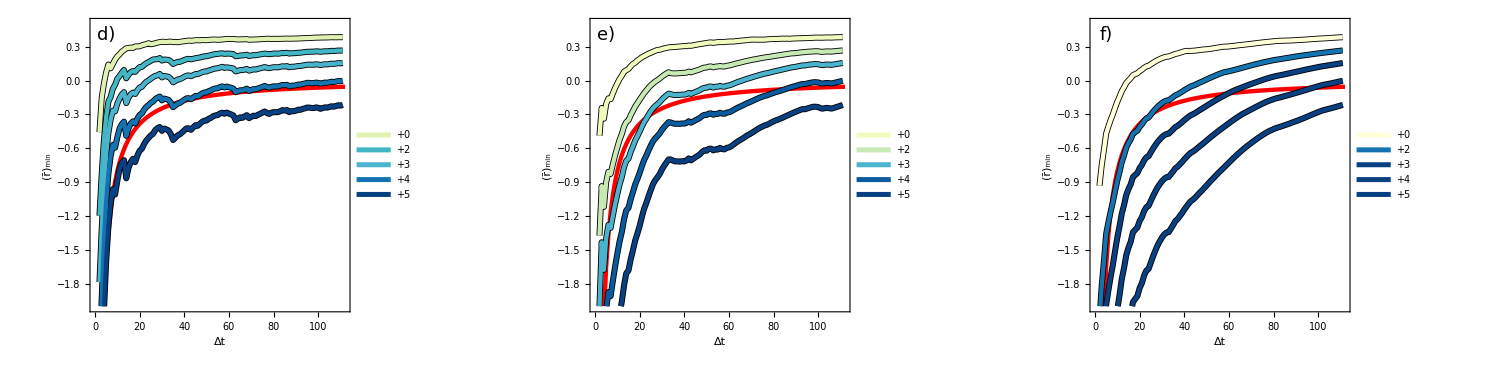

```mathematica
ExtTime[t_,α_,N0_]:=r/.NSolve[1==N0 r/α Exp[r t]/(((r/α)-N0)+N0 Exp[r t]),r,Reals][[1]];

white=Table[{i,Min[MovingAverage[w[tempsequence],i]]},{i,2,Length[tempsequence]-1}];
pink=Table[{i,Min[MovingAverage[w[tempsequence2],i]]},{i,2,Length[tempsequence2]-1}];
brown=Table[{i,Min[MovingAverage[w[tempsequence3],i]]},{i,2,Length[tempsequence3]-1}];

white2=Table[{i,Min[MovingAverage[w[tempsequence+2],i]]},{i,2,Length[tempsequence]-1}];
pink2=Table[{i,Min[MovingAverage[w[tempsequence2+2],i]]},{i,2,Length[tempsequence2]-1}];
brown2=Table[{i,Min[MovingAverage[w[tempsequence3+2],i]]},{i,2,Length[tempsequence3]-1}];

white3=Table[{i,Min[MovingAverage[w[tempsequence+3],i]]},{i,2,Length[tempsequence]-1}];
pink3=Table[{i,Min[MovingAverage[w[tempsequence2+3],i]]},{i,2,Length[tempsequence2]-1}];
brown3=Table[{i,Min[MovingAverage[w[tempsequence3+3],i]]},{i,2,Length[tempsequence3]-1}];

white4=Table[{i,Min[MovingAverage[w[tempsequence+4],i]]},{i,2,Length[tempsequence]-1}];
pink4=Table[{i,Min[MovingAverage[w[tempsequence2+4],i]]},{i,2,Length[tempsequence2]-1}];
brown4=Table[{i,Min[MovingAverage[w[tempsequence3+4],i]]},{i,2,Length[tempsequence3]-1}];

white5=Table[{i,Min[MovingAverage[w[tempsequence+5],i]]},{i,2,Length[tempsequence]-1}];
pink5=Table[{i,Min[MovingAverage[w[tempsequence2+5],i]]},{i,2,Length[tempsequence2]-1}];
brown5=Table[{i,Min[MovingAverage[w[tempsequence3+5],i]]},{i,2,Length[tempsequence3]-1}];

imsize=310;
arat=.7;

wplot=Show[ListLinePlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,Length[tempsequence]}],PlotStyle->{Thickness[0.01],Red},PlotRange->{{0,Length[tempsequence]},{-2,.5}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},AspectRatio->arat,ImageSize->imsize,
Epilog->{Text[Style["d)",Black,18],{5,.4}]}],
ListLinePlot[{white,white2,white3,white4,white5},PlotStyle->{{Thickness[.014],Black}},PlotRange->{{0,Length[tempsequence]},{-2,.5}}],
ListLinePlot[{white,white2,white3,white4,white5},PlotLegends->Placed[{"+0","+2","+3","+4","+5"},{Right,Bottom}],PlotRange->{{0,Length[tempsequence]},{-2,.5}},
PlotStyle->Table[{Directive[newmap[point[[3]]]],Thickness[.01]},{point,wresults}]]];

pplot=Show[
ListLinePlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,Length[tempsequence]}],PlotStyle->{Thickness[0.01],Red},PlotRange->{{0,Length[tempsequence]},{-2,.5}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},AspectRatio->arat,ImageSize->imsize,
Epilog->{Text[Style["e)",Black,18],{5,.4}]}],
ListLinePlot[{pink,pink2,pink3,pink4,pink5},PlotStyle->{{Thickness[.014],Black}},PlotRange->{{0,Length[tempsequence]},{-2,.5}}],
ListLinePlot[{pink,pink2,pink3,pink4,pink5},PlotLegends->Placed[{"+0","+2","+3","+4","+5"},{Right,Bottom}],PlotRange->{{0,Length[tempsequence]},{-2,.5}},
PlotStyle->Table[{Directive[newmap[point[[3]]]],Thickness[.01]},{point,presults}]]];

bplot=Show[
ListLinePlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,Length[tempsequence]}],PlotStyle->{Thickness[0.01],Red},PlotRange->{{0,Length[tempsequence]},{-2,.5}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},AspectRatio->arat,ImageSize->imsize,
Epilog->{Text[Style["f)",Black,18],{5,.4}]}],
ListLinePlot[{brown,brown2,brown3,brown4,brown5},PlotStyle->{{Thickness[.014],Black}},PlotRange->{{0,Length[tempsequence]},{-2,.5}}],
ListLinePlot[{brown,brown2,brown3,brown4,brown5},PlotLegends->Placed[{"+0","+2","+3","+4","+5"},{Right,Bottom}],PlotRange->{{0,Length[tempsequence]},{-2,.5}},
PlotStyle->Table[{Directive[newmap[point[[3]]]],Thickness[.01]},{point,bresults}]]];

exttimeplots=GraphicsRow[{wplot,pplot,bplot},Spacings->0,ImageSize->1500]

Export[directory<>"exttimeplots.pdf",exttimeplots,ImageResolution->1000];
```

## Plot Experimental Results

Use this code to generate plots in the supplemental material S4. You will first need to download ‘experimentalresults.csv.’

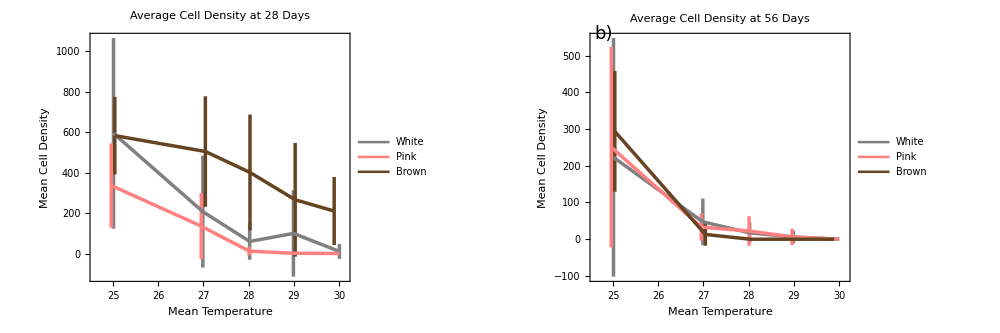

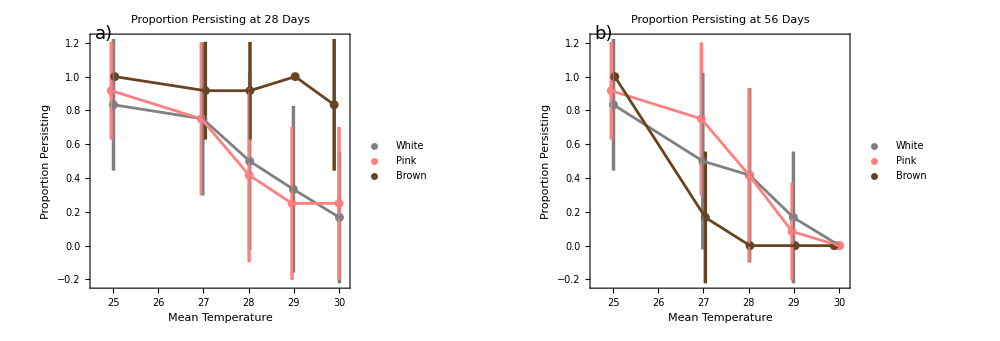

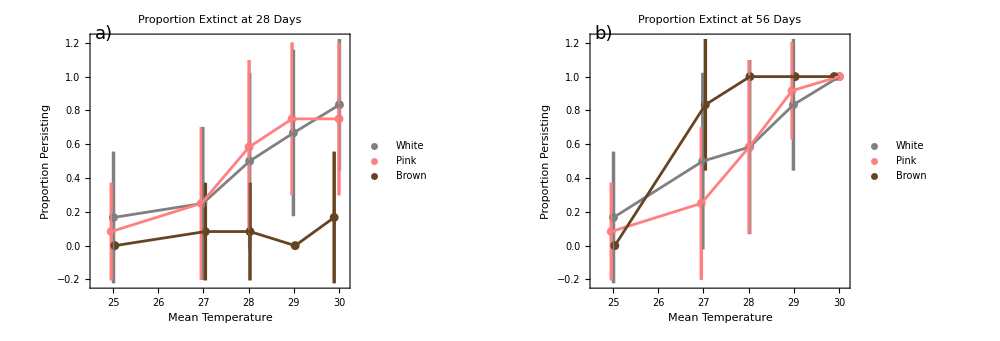

```mathematica
results=Import[directory<>"experimentalresults.csv","CSV"];

(*label all data*)
wmeantemps=results[[All,1]];
wsdtemps=results[[All,2]];
w28persist=results[[All,3]];
w56persist=results[[All,4]];
w28ext=results[[All,5]];
w56ext=results[[All,6]];
w28mpop=results[[All,7]];
w56mpop=results[[All,8]];
w28sdpop=results[[All,9]];
w56sdpop=results[[All,10]];

pmeantemps=results[[All,11]];
psdtemps=results[[All,12]];
p28persist=results[[All,13]];
p56persist=results[[All,14]];
p28ext=results[[All,15]];
p56ext=results[[All,16]];
p28mpop=results[[All,17]];
p56mpop=results[[All,18]];
p28sdpop=results[[All,19]];
p56sdpop=results[[All,20]];

bmeantemps=results[[All,21]];
bsdtemps=results[[All,22]];
b28persist=results[[All,23]];
b56persist=results[[All,24]];
b28ext=results[[All,25]];
b56ext=results[[All,26]];
b28mpop=results[[All,27]];
b56mpop=results[[All,28]];
b28sdpop=results[[All,29]];
b56sdpop=results[[All,30]];

w28extsd=results[[All,31]];
p28extsd=results[[All,32]];
b28extsd=results[[All,33]];
w56extsd=results[[All,34]];
p56extsd=results[[All,35]];
b56extsd=results[[All,36]];

(*pop density plots*)
w28density=Transpose[{wmeantemps,Around@@@Transpose[{w28mpop,w28sdpop}]}];
p28density=Transpose[{pmeantemps,Around@@@Transpose[{p28mpop,p28sdpop}]}];
b28density=Transpose[{bmeantemps,Around@@@Transpose[{b28mpop,b28sdpop}]}];
w56density=Transpose[{wmeantemps,Around@@@Transpose[{w56mpop,w56sdpop}]}];
p56density=Transpose[{pmeantemps,Around@@@Transpose[{p56mpop,p56sdpop}]}];
b56density=Transpose[{bmeantemps,Around@@@Transpose[{b56mpop,b56sdpop}]}];

thickness=.005;

density28=ListLinePlot[{w28density,p28density,b28density},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Average Cell Density at 28 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Right,Top}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Mean Cell Density"},LabelStyle->Directive[Black],ImageSize->500,
Epilog->{Text[Style["a)",Black,18],{24.8,1100}]}];
density56=ListLinePlot[{w56density,p56density,b56density},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Average Cell Density at 56 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Right,Top}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Mean Cell Density"},LabelStyle->Directive[Black],ImageSize->500,
Epilog->{Text[Style["b)",Black,18],{24.8,560}]}];
densities=GraphicsRow[{density28,density56},Spacings->0,ImageSize->1000]

(*persistence plots*)
w28p=Transpose[{wmeantemps,Around@@@Transpose[{w28persist,w28extsd}]}];
p28p=Transpose[{pmeantemps,Around@@@Transpose[{p28persist,p28extsd}]}];
b28p=Transpose[{bmeantemps,Around@@@Transpose[{b28persist,b28extsd}]}];
w56p=Transpose[{wmeantemps,Around@@@Transpose[{w56persist,w56extsd}]}];
p56p=Transpose[{pmeantemps,Around@@@Transpose[{p56persist,p56extsd}]}];
b56p=Transpose[{bmeantemps,Around@@@Transpose[{b56persist,b56extsd}]}];

persist28=Show[ListPlot[{w28p,p28p,b28p},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Persisting at 28 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Scaled[{0,0.32}],{0,0.5}}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,
Epilog->{Text[Style["a)",Black,18],{24.8,1.25}]}],ListLinePlot[{w28p,p28p,b28p},PlotStyle->{Gray,Pink,Darker[Brown]}]];
persist56=Show[ListPlot[{w56p,p56p,b56p},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Persisting at 56 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Right,Top}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,Epilog->{Text[Style["b)",Black,18],{24.8,1.25}]}],ListLinePlot[{w56p,p56p,b56p},PlotStyle->{Gray,Pink,Darker[Brown]}]];
persistence=GraphicsRow[{persist28,persist56},Spacings->0,ImageSize->1000]

(*extinction plots*)
w28e=Transpose[{wmeantemps,Around@@@Transpose[{w28ext,w28extsd}]}];
p28e=Transpose[{pmeantemps,Around@@@Transpose[{p28ext,p28extsd}]}];
b28e=Transpose[{bmeantemps,Around@@@Transpose[{b28ext,b28extsd}]}];
w56e=Transpose[{wmeantemps,Around@@@Transpose[{w56ext,w56extsd}]}];
p56e=Transpose[{pmeantemps,Around@@@Transpose[{p56ext,p56extsd}]}];
b56e=Transpose[{bmeantemps,Around@@@Transpose[{b56ext,b56extsd}]}];

extinct28=Show[ListPlot[{w28e,p28e,b28e},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Extinct at 28 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Scaled[{0,0.77}],{0,0.5}}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,Epilog->{Text[Style["a)",Black,18],{24.8,1.25}]}],ListLinePlot[{w28e,p28e,b28e},PlotStyle->{Gray,Pink,Darker[Brown]}]];
extinct56=Show[ListPlot[{w56e,p56e,b56e},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Extinct at 56 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Scaled[{0,0.77}],{0,0.5}}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,Epilog->{Text[Style["b)",Black,18],{24.8,1.25}]}],ListLinePlot[{w56e,p56e,b56e},PlotStyle->{Gray,Pink,Darker[Brown]}]];
extinct=GraphicsRow[{extinct28,extinct56},Spacings->0,ImageSize->1000]

Export[directory<>"densities.pdf",densities,"PDF",ImageResolution->1000];
Export[directory<>"persist.pdf",persistence,"PDF",ImageResolution->1000];
Export[directory<>"extinct.pdf",extinct,"PDF",ImageResolution->1000];
```

## SSA Comparison Across Different Time Series

Use this code to generate plots S6-8 (uses downloaded MX files of SSA outputs for these time series; you can calculate the spectral exponents using code in MethodsFigures.nb, and you can run the SSA model above with these time series to get these same results, but again, the code is quite slow).

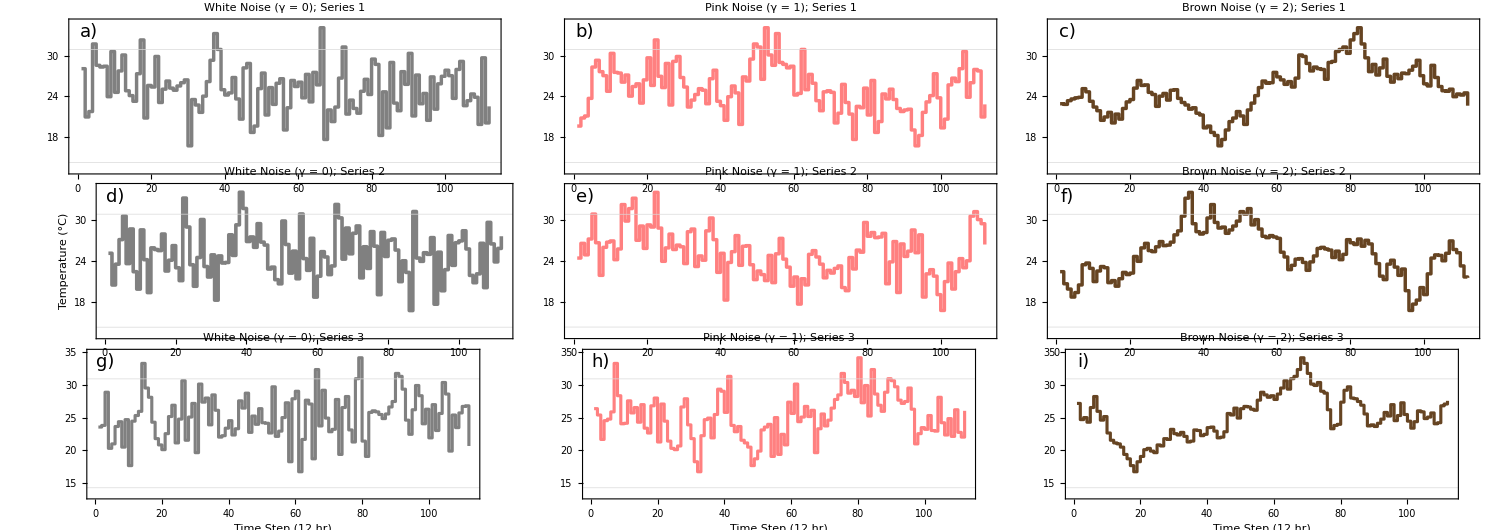

```mathematica
(*Fig S6; all time series listed out below, tempsequence, tempsequence2, and tempsequence3 are used in the main paper*)
tempsequence={28.105012956566068,20.973777168683974,21.777119582710675,31.756000496201537,28.600816667020446,28.344521382791513,28.47034266137066,23.96687349828974,30.63909206823437,24.607518315140997,27.770735127101812,30.12831827439933,24.843283381565694,24.129453086270793,23.289282561098656,27.360714125686286,32.350579224955645,20.818000065734736,25.63004329427447,25.392481684859003,29.90935651497313,23.110450057296283,25.078338674047963,26.281372248801993,25.235173241485796,24.921661325952037,25.550587396135597,26.03312650171026,26.450446653600267,16.710015292562446,23.549553346399733,22.736717716225108,21.655478617208487,24.048419981102587,26.19796757263583,29.34653377145162,33.289984707437554,30.947121810389547,25.,24.21002216148944,24.52858572096878,26.79954635260587,23.634488914372888,20.65346622854838,28.222880417289325,28.8780378716445,18.690399182412833,19.630578094766086,25.156716618434306,27.460010808216847,21.263503166426503,25.313748228765167,22.832426306719285,25.951580018897413,26.622977130100125,19.052878189610453,22.33516086609751,26.365511085627112,25.47141427903122,26.115237773875315,23.80203242736417,27.263282283774892,23.20045364739413,27.561328293508662,25.709825270812722,34.151719694604665,17.649420775044355,22.009434104564036,20.29191678038176,22.438671706491338,26.710717438901344,31.309600817587167,21.399183332979554,23.463754792880312,22.229264872898188,21.52965733862934,24.764826758514204,26.536245207119688,24.290174729187278,29.521278215385287,28.736496833573497,18.243999503798463,24.686251771234833,19.36090793176563,29.026222831316026,23.01917912323498,21.894987043433932,27.66483913390249,25.78997783851056,30.369421905233914,21.1219621283555,27.167573693280715,22.926540726162184,24.449412603864403,20.478721784614713,26.889549942703717,22.120769481240764,25.870546913729207,26.98082087676502,27.879230518759236,27.073459273837816,23.718627751198007,27.990565895435964,29.181999934265264,22.639285874313714,23.377022869899875,24.36995670572553,23.884762226124685,19.87168172560067,29.70808321961824,20.09064348502687,22.539989191783153};
tempsequence2={19.630578094766086,20.818000065734736,21.1219621283555,23.718627751198007,28.344521382791513,29.34653377145162,27.66483913390249,27.073459273837816,24.764826758514204,30.369421905233914,27.561328293508662,27.460010808216847,26.115237773875315,27.167573693280715,24.048419981102587,25.47141427903122,25.870546913729207,23.01917912323498,26.450446653600267,29.70808321961824,25.63004329427447,32.350579224955645,26.98082087676502,25.313748228765167,28.8780378716445,22.736717716225108,29.181999934265264,29.90935651497313,26.79954635260587,25.392481684859003,22.438671706491338,23.463754792880312,24.290174729187278,25.156716618434306,24.921661325952037,22.926540726162184,26.622977130100125,27.879230518759236,23.289282561098656,22.639285874313714,20.478721784614713,23.96687349828974,25.550587396135597,24.52858572096878,19.87168172560067,26.889549942703717,26.281372248801993,29.521278215385287,31.756000496201537,31.309600817587167,26.536245207119688,34.151719694604665,30.12831827439933,28.600816667020446,33.289984707437554,29.026222831316026,28.736496833573497,28.222880417289325,28.47034266137066,24.21002216148944,24.449412603864403,30.947121810389547,25.,27.263282283774892,25.951580018897413,23.377022869899875,21.894987043433932,24.686251771234833,24.843283381565694,24.607518315140997,20.09064348502687,21.52965733862934,25.78997783851056,23.110450057296283,21.399183332979554,17.649420775044355,22.539989191783153,22.33516086609751,25.235173241485796,21.263503166426503,26.365511085627112,18.690399182412833,20.29191678038176,24.36995670572553,23.634488914372888,25.078338674047963,23.549553346399733,22.229264872898188,21.777119582710675,22.009434104564036,22.120769481240764,19.052878189610453,16.710015292562446,18.243999503798463,21.655478617208487,23.20045364739413,24.129453086270793,27.360714125686286,23.80203242736417,19.36090793176563,20.65346622854838,25.709825270812722,26.710717438901344,26.19796757263583,28.105012956566068,30.63909206823437,23.884762226124685,26.03312650171026,27.990565895435964,27.770735127101812,20.973777168683974,22.832426306719285};
tempsequence3={22.926540726162184,22.832426306719285,23.377022869899875,23.634488914372888,23.80203242736417,23.884762226124685,25.156716618434306,24.686251771234833,23.289282561098656,22.438671706491338,21.894987043433932,20.478721784614713,20.973777168683974,21.655478617208487,20.09064348502687,21.399183332979554,20.65346622854838,22.229264872898188,23.20045364739413,23.549553346399733,25.235173241485796,26.365511085627112,25.63004329427447,25.709825270812722,24.607518315140997,24.290174729187278,22.539989191783153,24.048419981102587,24.449412603864403,23.463754792880312,24.921661325952037,25.,23.718627751198007,23.110450057296283,22.736717716225108,22.120769481240764,22.33516086609751,21.52965733862934,21.263503166426503,19.36090793176563,19.630578094766086,18.690399182412833,18.243999503798463,16.710015292562446,17.649420775044355,19.052878189610453,20.29191678038176,20.818000065734736,21.777119582710675,21.1219621283555,19.87168172560067,22.009434104564036,23.01917912323498,24.129453086270793,25.313748228765167,26.281372248801993,25.951580018897413,26.03312650171026,27.561328293508662,26.889549942703717,26.450446653600267,25.78997783851056,26.19796757263583,25.392481684859003,26.710717438901344,30.12831827439933,29.90935651497313,28.8780378716445,27.770735127101812,28.344521382791513,28.105012956566068,27.990565895435964,26.536245207119688,29.026222831316026,29.181999934265264,30.63909206823437,30.947121810389547,31.309600817587167,30.369421905233914,32.350579224955645,33.289984707437554,34.151719694604665,31.756000496201537,29.70808321961824,27.66483913390249,28.736496833573497,27.167573693280715,28.222880417289325,29.521278215385287,26.98082087676502,26.115237773875315,27.263282283774892,26.622977130100125,27.460010808216847,27.360714125686286,27.879230518759236,28.47034266137066,29.34653377145162,27.073459273837816,25.870546913729207,25.550587396135597,28.600816667020446,26.79954635260587,25.47141427903122,24.843283381565694,24.764826758514204,25.078338674047963,23.96687349828974,24.36995670572553,24.21002216148944,24.52858572096878,22.639285874313714};

Z0={25.156716618434306,20.478721784614713,23.549553346399733,27.167573693280715,30.63909206823437,23.634488914372888,28.736496833573497,22.438671706491338,19.87168172560067,28.600816667020446,24.21002216148944,19.36090793176563,25.951580018897413,25.709825270812722,25.550587396135597,27.990565895435964,22.539989191783153,24.129453086270793,26.281372248801993,23.01917912323498,21.1219621283555,33.289984707437554,29.026222831316026,23.463754792880312,20.29191678038176,24.52858572096878,30.12831827439933,23.20045364739413,21.655478617208487,24.921661325952037,18.243999503798463,24.764826758514204,23.718627751198007,23.80203242736417,27.879230518759236,24.843283381565694,29.34653377145162,34.151719694604665,31.756000496201537,26.889549942703717,27.561328293508662,26.03312650171026,29.521278215385287,26.79954635260587,26.365511085627112,22.832426306719285,23.110450057296283,21.263503166426503,20.65346622854838,29.90935651497313,26.450446653600267,22.229264872898188,25.47141427903122,21.399183332979554,30.947121810389547,24.36995670572553,22.639285874313714,27.360714125686286,18.690399182412833,21.777119582710675,25.392481684859003,24.607518315140997,22.009434104564036,23.289282561098656,32.350579224955645,30.369421905233914,24.290174729187278,28.8780378716445,25.078338674047963,28.105012956566068,29.181999934265264,21.52965733862934,26.115237773875315,22.926540726162184,28.344521382791513,26.19796757263583,19.052878189610453,28.222880417289325,24.686251771234833,27.073459273837816,27.263282283774892,25.63004329427447,20.973777168683974,24.048419981102587,22.33516086609751,16.710015292562446,31.309600817587167,24.449412603864403,23.96687349828974,25.235173241485796,25.,27.460010808216847,17.649420775044355,25.313748228765167,19.630578094766086,22.736717716225108,27.770735127101812,23.377022869899875,26.710717438901344,26.98082087676502,28.47034266137066,25.78997783851056,21.894987043433932,20.818000065734736,22.120769481240764,26.622977130100125,20.09064348502687,29.70808321961824,26.536245207119688,23.884762226124685,25.870546913729207,27.66483913390249};
Z1={24.449412603864403,26.622977130100125,24.921661325952037,27.263282283774892,30.947121810389547,26.710717438901344,21.894987043433932,26.03312650171026,26.79954635260587,26.98082087676502,24.21002216148944,25.78997783851056,32.350579224955645,29.90935651497313,31.756000496201537,33.289984707437554,27.073459273837816,29.181999934265264,25.870546913729207,29.34653377145162,29.026222831316026,34.151719694604665,28.8780378716445,23.96687349828974,25.951580018897413,27.990565895435964,25.709825270812722,26.365511085627112,26.115237773875315,23.634488914372888,28.344521382791513,28.736496833573497,23.20045364739413,24.764826758514204,24.129453086270793,28.47034266137066,30.369421905233914,27.167573693280715,22.33516086609751,25.156716618434306,18.243999503798463,23.80203242736417,25.392481684859003,27.770735127101812,23.377022869899875,26.19796757263583,26.281372248801993,23.463754792880312,21.263503166426503,22.539989191783153,22.009434104564036,21.1219621283555,24.843283381565694,20.818000065734736,25.078338674047963,27.360714125686286,24.290174729187278,23.110450057296283,20.29191678038176,21.655478617208487,17.649420775044355,21.399183332979554,20.478721784614713,25.,25.550587396135597,24.607518315140997,23.549553346399733,21.52965733862934,22.639285874313714,22.229264872898188,22.926540726162184,23.289282561098656,20.09064348502687,19.630578094766086,24.52858572096878,22.832426306719285,25.63004329427447,25.313748228765167,29.70808321961824,27.66483913390249,28.222880417289325,27.460010808216847,27.561328293508662,28.105012956566068,20.65346622854838,23.884762226124685,26.889549942703717,19.36090793176563,26.536245207119688,24.686251771234833,25.47141427903122,28.600816667020446,25.235173241485796,27.879230518759236,18.690399182412833,22.120769481240764,22.736717716225108,21.777119582710675,19.052878189610453,16.710015292562446,20.973777168683974,23.718627751198007,19.87168172560067,22.438671706491338,24.36995670572553,23.01917912323498,24.048419981102587,30.63909206823437,31.309600817587167,30.12831827439933,29.521278215385287,26.450446653600267};
Z2={22.438671706491338,20.65346622854838,19.87168172560067,18.690399182412833,19.36090793176563,20.478721784614713,23.463754792880312,23.718627751198007,22.926540726162184,20.973777168683974,22.539989191783153,23.20045364739413,23.01917912323498,20.818000065734736,21.1219621283555,20.29191678038176,21.399183332979554,22.33516086609751,22.009434104564036,22.229264872898188,24.686251771234833,23.96687349828974,25.951580018897413,26.622977130100125,25.550587396135597,25.392481684859003,26.115237773875315,26.889549942703717,26.281372248801993,26.365511085627112,26.79954635260587,27.879230518759236,28.47034266137066,30.63909206823437,33.289984707437554,34.151719694604665,29.521278215385287,28.344521382791513,27.990565895435964,28.222880417289325,30.369421905233914,32.350579224955645,29.70808321961824,28.8780378716445,29.026222831316026,28.105012956566068,28.600816667020446,29.181999934265264,29.90935651497313,31.309600817587167,30.947121810389547,31.756000496201537,29.34653377145162,30.12831827439933,28.736496833573497,27.66483913390249,27.460010808216847,27.770735127101812,27.561328293508662,27.360714125686286,25.313748228765167,24.607518315140997,22.736717716225108,23.377022869899875,24.290174729187278,24.36995670572553,23.80203242736417,22.639285874313714,23.884762226124685,24.764826758514204,25.870546913729207,26.03312650171026,25.78997783851056,25.63004329427447,24.52858572096878,25.47141427903122,24.21002216148944,25.,27.167573693280715,26.710717438901344,26.450446653600267,27.263282283774892,26.19796757263583,27.073459273837816,26.536245207119688,25.078338674047963,23.634488914372888,21.777119582710675,21.263503166426503,23.549553346399733,24.129453086270793,23.110450057296283,21.894987043433932,22.832426306719285,19.630578094766086,16.710015292562446,17.649420775044355,18.243999503798463,20.09064348502687,19.052878189610453,22.120769481240764,24.449412603864403,24.921661325952037,24.843283381565694,24.048419981102587,25.156716618434306,26.98082087676502,25.709825270812722,25.235173241485796,23.289282561098656,21.655478617208487,21.52965733862934};

Z0two={23.549553346399733,23.80203242736417,28.8780378716445,20.29191678038176,20.973777168683974,23.634488914372888,24.36995670572553,20.478721784614713,24.686251771234833,17.649420775044355,24.449412603864403,25.313748228765167,25.951580018897413,33.289984707437554,29.521278215385287,28.105012956566068,24.290174729187278,21.777119582710675,20.818000065734736,20.09064348502687,22.539989191783153,25.156716618434306,26.889549942703717,21.1219621283555,24.764826758514204,30.63909206823437,21.52965733862934,25.078338674047963,27.167573693280715,19.630578094766086,30.12831827439933,27.360714125686286,27.990565895435964,23.884762226124685,28.47034266137066,26.115237773875315,22.009434104564036,22.229264872898188,23.377022869899875,24.52858572096878,22.33516086609751,23.289282561098656,27.561328293508662,26.450446653600267,28.736496833573497,22.736717716225108,25.235173241485796,23.96687349828974,26.365511085627112,24.21002216148944,24.129453086270793,22.639285874313714,29.70808321961824,22.120769481240764,22.926540726162184,25.,27.263282283774892,18.243999503798463,27.879230518759236,29.026222831316026,16.710015292562446,21.655478617208487,27.66483913390249,27.073459273837816,18.690399182412833,32.350579224955645,23.718627751198007,29.181999934265264,24.921661325952037,22.832426306719285,23.20045364739413,27.770735127101812,19.36090793176563,26.536245207119688,28.222880417289325,23.110450057296283,21.263503166426503,30.947121810389547,34.151719694604665,21.399183332979554,19.052878189610453,25.78997783851056,26.03312650171026,25.870546913729207,25.47141427903122,24.843283381565694,25.550587396135597,26.622977130100125,27.460010808216847,31.756000496201537,31.309600817587167,29.34653377145162,24.607518315140997,22.438671706491338,26.19796757263583,29.90935651497313,28.344521382791513,24.048419981102587,26.281372248801993,21.894987043433932,26.98082087676502,23.01917912323498,25.63004329427447,30.369421905233914,28.600816667020446,19.87168172560067,25.392481684859003,23.463754792880312,25.709825270812722,26.710717438901344,26.79954635260587,20.65346622854838};
Z1two={26.365511085627112,25.392481684859003,21.655478617208487,24.52858572096878,24.764826758514204,25.870546913729207,33.289984707437554,28.344521382791513,24.048419981102587,24.129453086270793,27.561328293508662,25.709825270812722,26.536245207119688,24.290174729187278,26.98082087676502,23.377022869899875,22.639285874313714,26.79954635260587,27.990565895435964,21.263503166426503,27.073459273837816,24.449412603864403,21.399183332979554,20.29191678038176,20.09064348502687,20.65346622854838,26.622977130100125,27.879230518759236,23.884762226124685,21.777119582710675,18.243999503798463,16.710015292562446,22.229264872898188,24.686251771234833,24.921661325952037,21.894987043433932,25.47141427903122,29.34653377145162,29.026222831316026,25.78997783851056,31.309600817587167,23.80203242736417,22.832426306719285,23.634488914372888,21.52965733862934,21.1219621283555,20.478721784614713,17.649420775044355,18.690399182412833,19.87168172560067,23.110450057296283,23.549553346399733,23.96687349828974,19.052878189610453,25.,19.36090793176563,22.438671706491338,20.818000065734736,27.360714125686286,25.63004329427447,30.12831827439933,24.36995670572553,25.078338674047963,26.710717438901344,25.156716618434306,26.115237773875315,19.630578094766086,23.289282561098656,25.550587396135597,23.718627751198007,24.607518315140997,26.450446653600267,27.770735127101812,28.47034266137066,31.756000496201537,30.369421905233914,28.736496833573497,29.181999934265264,28.222880417289325,34.151719694604665,27.263282283774892,29.90935651497313,25.235173241485796,32.350579224955645,28.600816667020446,26.889549942703717,25.951580018897413,28.8780378716445,30.947121810389547,30.63909206823437,29.70808321961824,27.66483913390249,27.167573693280715,27.460010808216847,29.521278215385287,26.281372248801993,20.973777168683974,22.539989191783153,23.463754792880312,23.20045364739413,25.313748228765167,23.01917912323498,22.926540726162184,28.105012956566068,24.21002216148944,22.33516086609751,24.843283381565694,22.120769481240764,26.19796757263583,22.736717716225108,22.009434104564036,26.03312650171026};
Z2two={27.167573693280715,24.686251771234833,25.,24.290174729187278,26.536245207119688,28.222880417289325,25.951580018897413,24.607518315140997,25.156716618434306,22.639285874313714,21.52965733862934,21.1219621283555,20.973777168683974,20.478721784614713,19.36090793176563,18.690399182412833,17.649420775044355,16.710015292562446,18.243999503798463,19.052878189610453,20.09064348502687,20.29191678038176,19.87168172560067,19.630578094766086,20.818000065734736,20.65346622854838,21.777119582710675,21.655478617208487,23.20045364739413,22.539989191783153,22.33516086609751,22.736717716225108,22.120769481240764,21.263503166426503,21.399183332979554,23.110450057296283,23.01917912323498,22.229264872898188,22.438671706491338,23.463754792880312,23.549553346399733,22.926540726162184,21.894987043433932,22.009434104564036,22.832426306719285,25.63004329427447,25.392481684859003,26.450446653600267,24.921661325952037,26.365511085627112,26.710717438901344,26.622977130100125,26.281372248801993,26.115237773875315,27.66483913390249,28.8780378716445,28.47034266137066,28.105012956566068,28.344521382791513,27.770735127101812,28.600816667020446,29.521278215385287,30.63909206823437,29.34653377145162,30.947121810389547,31.309600817587167,32.350579224955645,34.151719694604665,33.289984707437554,31.756000496201537,30.12831827439933,29.90935651497313,30.369421905233914,29.026222831316026,28.736496833573497,26.19796757263583,23.289282561098656,23.80203242736417,23.96687349828974,27.360714125686286,29.181999934265264,29.70808321961824,27.990565895435964,27.879230518759236,27.460010808216847,26.889549942703717,25.550587396135597,23.718627751198007,23.884762226124685,23.634488914372888,24.129453086270793,24.764826758514204,25.78997783851056,25.235173241485796,26.98082087676502,24.52858572096878,25.313748228765167,27.263282283774892,25.47141427903122,24.449412603864403,23.377022869899875,24.36995670572553,26.03312650171026,25.870546913729207,24.843283381565694,25.078338674047963,25.709825270812722,24.048419981102587,24.21002216148944,26.79954635260587,27.073459273837816,27.561328293508662};

thickness=.005;
Tmax=30.92;
Tmin=14.26;

compareserieswhite=ListLinePlot[{tempsequence,Z0,Z0two},InterpolationOrder->0,ImageSize->450,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Darker[Gray]},Black},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLegends->Placed[{"series1","series2","series3"},{Left,Bottom}],PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)","Temperature (°C)"},FrameStyle->16];
compareseriespink=ListLinePlot[{tempsequence2,Z1,Z1two},InterpolationOrder->0,ImageSize->450,PlotStyle->{{Thickness[thickness],Pink},{Thickness[thickness],Red},Black},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLegends->Placed[{"series1","series2","series3"},{Left,Bottom}],PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)","Temperature (°C)"},FrameStyle->16];
compareseriesbrown=ListLinePlot[{tempsequence3,Z2,Z2two},InterpolationOrder->0,ImageSize->450,PlotStyle->{{Thickness[thickness],Brown},{Thickness[thickness],Darker[Darker[Brown]]},Black},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLegends->Placed[{"series1","series2","series3"},{Left,Bottom}],PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)","Temperature (°C)"},FrameStyle->16];

white1=ListLinePlot[{tempsequence},InterpolationOrder->0,ImageSize->495,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Darker[Gray]},Black},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"White Noise (γ = 0); Series 1",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{None,None},FrameStyle->16,
Epilog->{Text[Style["a)",Black,18],{3,33.5}]}];
white2=ListLinePlot[{Z0},InterpolationOrder->0,ImageSize->520,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Darker[Gray]},Black},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"White Noise (γ = 0); Series 2",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{None,"Temperature (°C)"},FrameStyle->16,
Epilog->{Text[Style["d)",Black,18],{3,33.5}]}];
white3=ListLinePlot[{Z0two},InterpolationOrder->0,ImageSize->450,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Darker[Gray]},Black},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"White Noise (γ = 0); Series 3",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)",None},FrameStyle->16,
Epilog->{Text[Style["g)",Black,18],{3,33.5}]}];

pink1=ListLinePlot[{tempsequence2},InterpolationOrder->0,ImageSize->495,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Pink}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"Pink Noise (γ = 1); Series 1",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{None,None},FrameStyle->16,
Epilog->{Text[Style["b)",Black,18],{3,33.5}]}];
pink2=ListLinePlot[{Z1},InterpolationOrder->0,ImageSize->495,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Pink}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"Pink Noise (γ = 1); Series 2",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{None,None},FrameStyle->16,
Epilog->{Text[Style["e)",Black,18],{3,33.5}]}];
pink3=ListLinePlot[{Z1two},InterpolationOrder->0,ImageSize->450,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Pink}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"Pink Noise (γ = 1); Series 3",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)",None},FrameStyle->16,
Epilog->{Text[Style["h)",Black,18],{3,33.5}]}];

brown1=ListLinePlot[{tempsequence3},InterpolationOrder->0,ImageSize->495,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Darker[Brown]}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"Brown Noise (γ = 2); Series 1",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{None,None},FrameStyle->16,
Epilog->{Text[Style["c)",Black,18],{3,33.5}]}];
brown2=ListLinePlot[{Z2},InterpolationOrder->0,ImageSize->495,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Darker[Brown]}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"Brown Noise (γ = 2); Series 2",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{None,None},FrameStyle->16,
Epilog->{Text[Style["f)",Black,18],{3,33.5}]}];
brown3=ListLinePlot[{Z2two},InterpolationOrder->0,ImageSize->450,AspectRatio->.3,PlotStyle->{{Thickness[thickness],Darker[Brown]}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},PlotLabel->"Brown Noise (γ = 2); Series 3",PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)",None},FrameStyle->16,
Epilog->{Text[Style["i)",Black,18],{3,33.5}]}];

compareSSAseries=GraphicsGrid[{{white1,pink1,brown1},{white2,pink2,brown2},{white3,pink3,brown3}},ImageSize->1500,Spacings->-25]
Export[directory<>"compareseries.pdf",compareSSAseries,"PDF",ImageResolution->800];
```

```mathematica
(*generate compison plots of SSA outcomes, Figs S7-8*)
(*import SSA outputs for the three different sets of time series above*)
SSAwhite=Import[directory<>"SSA2_white.m","MX"];
SSApink=Import[directory<>"SSA2_pink.m","MX"];
SSAbrown=Import[directory<>"SSA2_brown.m","MX"];

(*draw persistence boundaries*)
lactin2[T_,{a_,b_,tmax_,δT_}]:=Exp[a T]-Exp[a tmax-((tmax-T)/δT)]+b;
paramsfit={0.044,-1.774,35.254,5.435};
w[T_]:=lactin2[T,paramsfit];
divisions=40;
σTrange=Range[0.01,8.01,8/divisions];
μTrange=Range[10,35,25/divisions];

Clear[T];
moments=Flatten[ParallelTable[Module[{mean,var,skew,kurt},
mean=NExpectation[w[T],T\[Distributed]NormalDistribution[μT,σT]];
var=NExpectation[(w[T]-mean)^2,T\[Distributed]NormalDistribution[μT,σT]];
skew=NExpectation[((w[T]-mean))^3,T\[Distributed]NormalDistribution[μT,σT]]/var^(3/2);
kurt=NExpectation[(w[T]-mean)^4,T\[Distributed]NormalDistribution[μT,σT]]/(var^2)-3;
{μT,σT,mean,var,skew,kurt,If[mean>0,Log10[var/mean],10]}],{σT,σTrange},{μT,μTrange}],1];

newmap[x_]:=Blend[{RGBColor["#ffffd9"],RGBColor["#edf8b1"],RGBColor["#c7e9b4"],RGBColor["#7fcdbb"],RGBColor["#41b6c4"],RGBColor["#4eb3d3"],RGBColor["#2b8cbe"],RGBColor["#0868ac"],RGBColor["#084081"]},1-x];

(*plot outputs*)
SSAwhiteplot=Show[ListContourPlot[SSAwhite,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0); Series 1",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["a)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot=Show[ListContourPlot[SSApink,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1); Series 1",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["b)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot=Show[ListContourPlot[SSAbrown,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2); Series 1",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["c)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAwhite2=Import[directory<>"SSA_timeseries2_white.m","MX"];
SSApink2=Import[directory<>"SSA_timeseries2_pink.m","MX"];
SSAbrown2=Import[directory<>"SSA_timeseries2_brown.m","MX"];

SSAwhiteplot2=Show[ListContourPlot[SSAwhite2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0); Series 2",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["d)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot2=Show[ListContourPlot[SSApink2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1); Series 2",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["e)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot2=Show[ListContourPlot[SSAbrown2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2); Series 2",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["f)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAwhite3=Import[directory<>"SSA_timeseries3_white.m","MX"];
SSApink3=Import[directory<>"SSA_timeseries3_pink.m","MX"];
SSAbrown3=Import[directory<>"SSA_timeseries3_brown.m","MX"];

SSAwhiteplot3=Show[ListContourPlot[SSAwhite3,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0); Series 3",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["g)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot3=Show[ListContourPlot[SSApink3,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1); Series 3",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["h)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot3=Show[ListContourPlot[SSAbrown3,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2); Series 3",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["i)",White,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAs=GraphicsGrid[{{SSAwhiteplot,SSApinkplot,SSAbrownplot},{SSAwhiteplot2,SSApinkplot2,SSAbrownplot2},{SSAwhiteplot3,SSApinkplot3,SSAbrownplot3}},Spacings->0,ImageSize->1000]
(*Export[directory<>"S7.pdf",SSAs,"PDF",ImageResolution->800]*)

(*DIFFERENCE PLOTS*)
(*matrices are not indexed in the same order for some reason; sort outputs by the same index here*)
sortedw1=SortBy[SSAwhite,{#[[1]],#[[2]]}&];
sortedw2=SortBy[SSAwhite2,{#[[1]],#[[2]]}&];
sortedw3=SortBy[SSAwhite3,{#[[1]],#[[2]]}&];
sortedp1=SortBy[SSApink,{#[[1]],#[[2]]}&];
sortedp2=SortBy[SSApink2,{#[[1]],#[[2]]}&];
sortedp3=SortBy[SSApink3,{#[[1]],#[[2]]}&];
sortedb1=SortBy[SSAbrown,{#[[1]],#[[2]]}&];
sortedb2=SortBy[SSAbrown2,{#[[1]],#[[2]]}&];
sortedb3=SortBy[SSAbrown3,{#[[1]],#[[2]]}&];

(*calculate differences between outputs*)
diffw12=sortedw1[[All,3]]-sortedw2[[All,3]];
SSAw12=Transpose[{sortedw1[[All,1]],sortedw1[[All,2]],diffw12}];
diffp12=sortedp1[[All,3]]-sortedp2[[All,3]];
SSAp12=Transpose[{sortedw1[[All,1]],sortedw1[[All,2]],diffp12}];
diffb12=sortedb1[[All,3]]-sortedb2[[All,3]];
SSAb12=Transpose[{sortedw1[[All,1]],sortedw1[[All,2]],diffb12}];

diffw13=sortedw1[[All,3]]-sortedw3[[All,3]];
SSAw13=Transpose[{sortedw1[[All,1]],sortedw1[[All,2]],diffw13}];
diffp13=sortedp1[[All,3]]-sortedp3[[All,3]];
SSAp13=Transpose[{sortedw1[[All,1]],sortedw1[[All,2]],diffp13}];
diffb13=sortedb1[[All,3]]-sortedb3[[All,3]];
SSAb13=Transpose[{sortedw1[[All,1]],sortedw1[[All,2]],diffb13}];

(*align color scales across plots; attempt to make 0 approximately white (not quite successful, but close)*)
vals={SSAw12[[All,3]],SSAp12[[All,3]],SSAb12[[All,3]],SSAw13[[All,3]],SSAp13[[All,3]],SSAb13[[All,3]]};
maxAbs=Max[Abs[vals]];
minVal=-maxAbs;
maxVal=maxAbs;
contours=Subdivide[minVal,maxVal,19];
newmap2[z_]:=Module[{v=z},v=Clip[v,{minVal,maxVal}];Which[v<0,Blend[{Blue,White},(v-minVal)/(0-minVal)],v>0,Blend[{White,Red},(v-0)/(maxVal-0)],True,White]];

(*plot outputs*)
compwhite2=Show[ListContourPlot[SSAw12,InterpolationOrder->0,Contours->19,PlotRange->{minVal,maxVal},ColorFunction->newmap2,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,All],Left],(*Placed[Automatic,Left]*)PlotLabel->Style["White Noise (γ = 0); Series 1-2",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["a)",Black,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];
comppink2=Show[ListContourPlot[SSAp12,InterpolationOrder->0,Contours->19,PlotRange->{minVal,maxVal},ColorFunction->newmap2,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,All],Left],PlotLabel->Style["Pink Noise (γ = 1); Series 1-2",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["b)",Black,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];
compbrown2=Show[ListContourPlot[SSAb12,InterpolationOrder->0,Contours->19,PlotRange->{minVal,maxVal},ColorFunction->newmap2,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,All],Left],PlotLabel->Style["Brown Noise (γ = 1); Series 1-2",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["c)",Black,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

compwhite3=Show[ListContourPlot[SSAw13,InterpolationOrder->0,Contours->19,PlotRange->{minVal,maxVal},ColorFunction->newmap2,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,All],Left],(*Placed[Automatic,Left]*)PlotLabel->Style["White Noise (γ = 0); Series 1-3",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["d)",Black,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];
comppink3=Show[ListContourPlot[SSAp13,InterpolationOrder->0,Contours->19,PlotRange->{minVal,maxVal},ColorFunction->newmap2,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,All],Left],PlotLabel->Style["Pink Noise (γ = 1); Series 1-3",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["e)",Black,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];
compbrown3=Show[ListContourPlot[SSAb13,InterpolationOrder->0,Contours->19,PlotRange->{minVal,maxVal},ColorFunction->newmap2,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,All],Left],PlotLabel->Style["Brown Noise (γ = 2); Series 1-3",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["f)",Black,17],{11.2,7.7}]}}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAdiffs=GraphicsGrid[{{compwhite2,comppink2,compbrown2},{compwhite3,comppink3,compbrown3}},Spacings->2,ImageSize->1150]
(*Export[directory<>"S8.pdf",SSAdiffs,"PDF",ImageResolution->800]*)
```

-Graphics-

-Graphics-